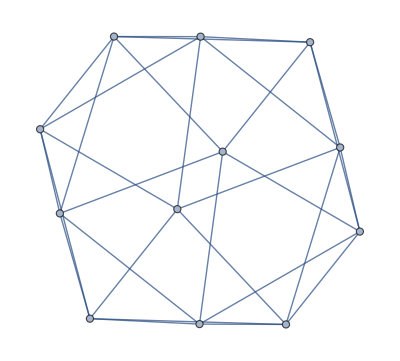

```mathematica
mainGraph = Graph[plantri[[1]]]
```

```mathematica
ChromaticPolynomial[mainGraph,4]/24
```

```mathematica
AreNeighbours[g_,vertices_]:=Block[{sets=Subsets[vertices,{2}],result=0},
Table[
result+=If[EdgeQ[g,e[[1]]<->e[[2]]],1,0]
,{e,sets}];
result]
```

```mathematica
Clear[mainGraph]
```

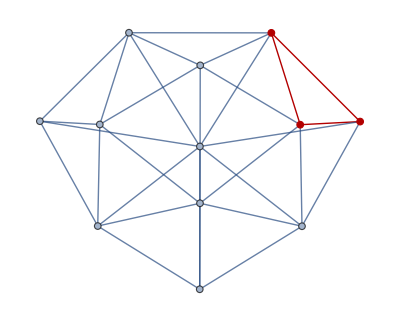
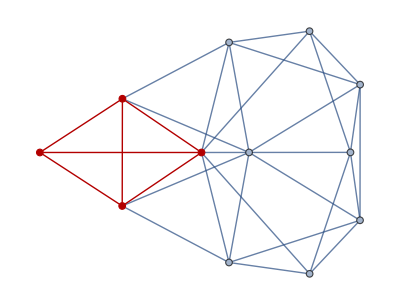
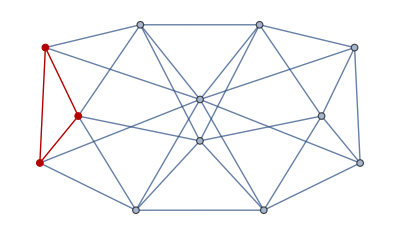
{{2,{1,2,3},7,-Graphics-,True,3},{2,{1,2,4},4,-Graphics-,True,2},{2,{1,2,5},16,-Graphics-,True,2}}

```mathematica
values=Monitor[
Flatten[
Table[
With[{mainGraph=Graph[plantri[[p]]]},
Table[
With[{g=VertexContract[mainGraph, vertices]},
{p,vertices, ChromaticPolynomial[g,4]/24,HighlightGraph[g,Subgraph[g,First[FindClique[g]]]],PlanarGraphQ[g],AreNeighbours[mainGraph,vertices]}
],{vertices,Subsets[VertexList[mainGraph],{3}]}]
],
{p,2,5}
],
1],
{p,vertices}
];Take[values,3]
```

```mathematica
AreNeighbours[Graph[plantri[[2]]],{1,2,3}]
```

3

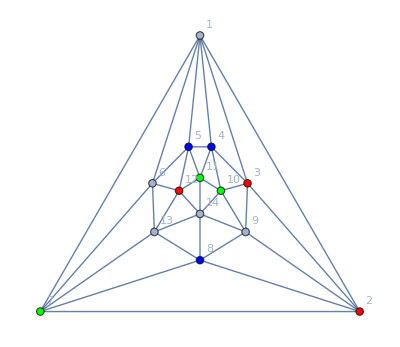

```mathematica
Graph[plantri[[2]],VertexStyle->{2->Red,3->Red,12->Red,4->Blue,5->Blue,8->Blue,7->Green,10->Green,11->Green},GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

```mathematica
Map[#[[6]]&,Select[values,#[[3]]!=0&]]//Tally
```

{{3,106},{2,357},{1,1023},{0,359}}

```mathematica
Map[#[[6]]&,Select[values,#[[3]]==0&]]//Tally
```

{{1,60},{0,34}}

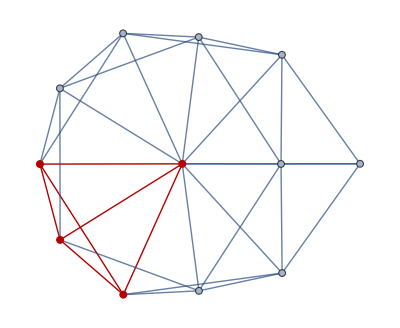
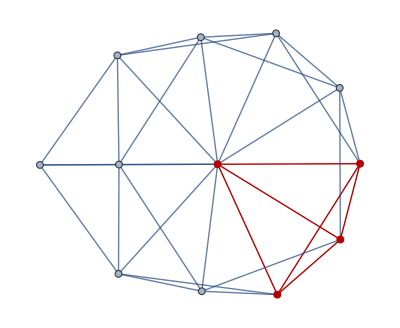
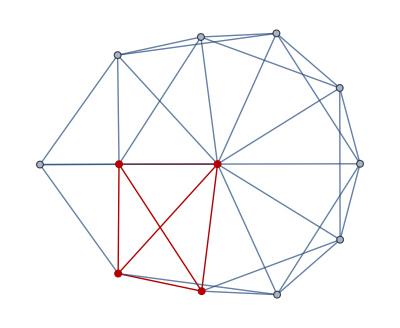
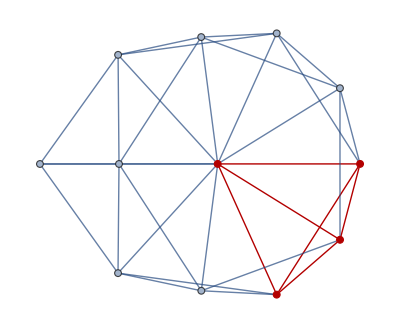
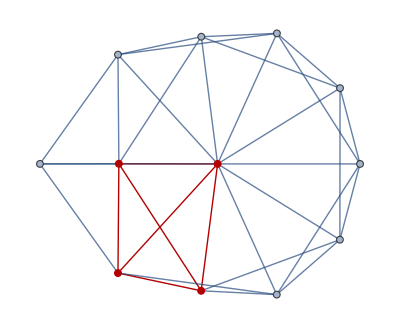
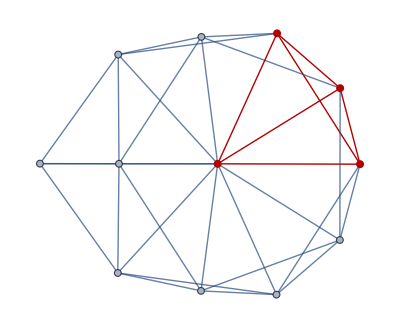
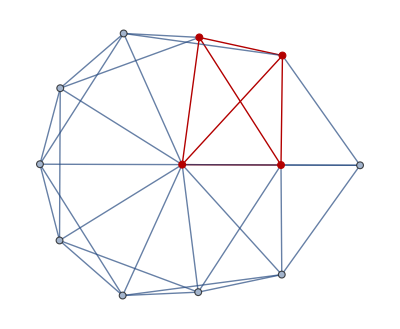
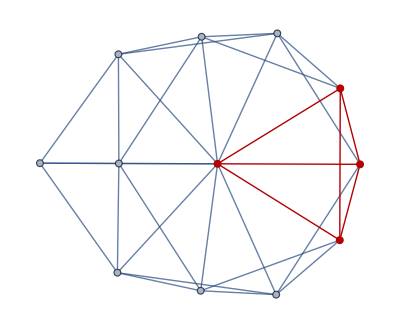
{{2,{2,3,12},0,-Graphics-,False,1},{2,{2,7,11},0,-Graphics-,False,1},{2,{2,11,12},0,-Graphics-,False,1},{2,{3,4,13},0,-Graphics-,False,1},{2,{3,12,13},0,-Graphics-,False,1},{2,{4,5,8},0,-Graphics-,False,1},{2,{4,8,13},0,-Graphics-,False,1},{2,{5,6,9},0,-Graphics-,False,1},{2,{5,8,9},0,-Graphics-,False,1},{2,{6,7,10},0,-Graphics-,False,1},{2,{6,9,10},0,-Graphics-,False,1},{2,{7,10,11},0,-Graphics-,False,1}}

```mathematica
Select[values,#[[3]]==0&]
```

```mathematica
FindClique[PetersenGraph[]]
```

{{1,3}}

```mathematica
TreeToCycle[g_]:=Block[{result,h, current,new},
h=g;
current=First[Select[VertexList[h],VertexDegree[g,#]==1&]];
result={current};
While[VertexCount[h]>1,

new=First[Select[EdgeList[h],First[#]==current||Last[#]==current&]];
new={new[[1]],new[[2]]};
new=Select[new,#≠current&]//First;
h=VertexDelete[h,current];
current=new;
result=Append[result,current];
];
result
];
```

```mathematica
Table[stubbornForm4[k]["graph"],{k,Take[Keys[stubbornForm4],5]}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

## This checks whether any 4-base can be embedded in an empty pentagon with a positive colofour

```mathematica
values789=Monitor[
Table[
Print["Starting ", p];
With[{mainGraph=Graph[plantri[[p]]]},
Table[
v->
With[{
span=FindSpanningTree[VertexDelete[NeighborhoodGraph[mainGraph,v],v]]
},
Table[
With[
{f=VertexDelete[EdgeDelete[mainGraph,EdgeList[span]],v]},
Table[
{h["signature"],
With[
{i=EmbedGraphPlantri[f,h,vert]},
With[
{val=
ChromaticPolynomial[i,4]/24},
If[val==0,Print["OEPS",p,"     ", v,"     ",vert, "     ", VertexList[span],"     ",h["signature"],"     ",Graph[i,GraphHighlight->vert,VertexLabels->"Name"]]];
{p,v,vert,h["signature"],val}
]
]}
,
{h,Table[stubbornForm4[k],{k,Sort[baseKeys4]}]}
]
]
,{vert,Subsets[VertexList[span],{4}]}
]
]

,{v,Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==5&]}
]
],
{p,19,23}
],
{p,v,vert,h["signature"]}
];
```

Starting 19

Starting 20

Starting 21

$Aborted[]

$Aborted[]

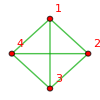
-Graphics-{364→v1x2x3x4,1}

```mathematica
CosyPrint4[364]
```

```mathematica
EmbedGraphPlantri[main_,val_,vertexList_]:=Block[{ sets, reference=vertexList, g, sub},
sets=val["vertexsets"];
g=main;
Table[If[Length[s]>1,
g=VertexContract[g,Table[reference[[v]],{v,s}]]
], {s,sets}];
sub=val["graph"];
Table[
g=EdgeAdd[g,{reference[[First[sets[[e[[1]]]]]]]<->reference[[First[sets[[e[[2]]]]]]]}],{e,EdgeList[sub]}];
g
]
```

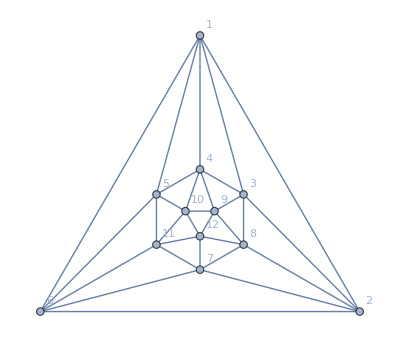

```mathematica
Graph[plantri[[1]],GraphLayout->"TutteEmbedding",VertexLabels->"Name"]
```

## This checks whether any 3-base can be embedded in an empty quadrilateral with a positive colofour

```mathematica
values789Three=Monitor[
Table[
Print["Starting ", p];
With[{mainGraph=ReadGrof[p]},
Table[
v->
With[{
span=FindSpanningTree[VertexDelete[NeighborhoodGraph[mainGraph,v],v]]
},
Table[
With[
{f=VertexDelete[EdgeDelete[mainGraph,EdgeList[span]],v]},
Table[
{h["signature"],
With[
{i=EmbedGraphPlantri[f,h,vert]},
With[
{val=
ChromaticPolynomial[i,4]/24},
If[val==0,Print["OEPS",p,"     ", v,"     ",vert, "     ", VertexList[span],"     ",h["signature"],"     ",Graph[i,GraphHighlight->vert,VertexLabels->"Name"]]];
{p,v,vert,h["signature"],val}
]
]}
,
{h,Table[stubbornForm3[k],{k,Sort[baseKeys3]}]}
]
]
,{vert,Subsets[VertexList[span],{3}]}
]
]

,{v,Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==4&]}
]
],
{p,1,1000}
],
{p,v,vert,h["signature"]}
];
```

Starting 1

Starting 2

Starting 3

Starting 4

Starting 5

Starting 6

Starting 7

Starting 8

Starting 9

Starting 10

Starting 11

Starting 12

Starting 13

Starting 14

Starting 15

Starting 16

Starting 17

Starting 18

Starting 19

Starting 20

Starting 21

Starting 22

Starting 23

Starting 24

Starting 25

Starting 26

Starting 27

Starting 28

Starting 29

Starting 30

Starting 31

Starting 32

Starting 33

Starting 34

Starting 35

Starting 36

Starting 37

Starting 38

Starting 39

Starting 40

Starting 41

Starting 42

Starting 43

Starting 44

Starting 45

Starting 46

Starting 47

Starting 48

Starting 49

Starting 50

Starting 51

Starting 52

Starting 53

Starting 54

Starting 55

Starting 56

Starting 57

Starting 58

Starting 59

Starting 60

Starting 61

Starting 62

Starting 63

Starting 64

Starting 65

Starting 66

Starting 67

Starting 68

Starting 69

Starting 70

Starting 71

Starting 72

Starting 73

Starting 74

Starting 75

Starting 76

Starting 77

Starting 78

Starting 79

Starting 80

Starting 81

Starting 82

Starting 83

Starting 84

Starting 85

Starting 86

Starting 87

Starting 88

Starting 89

Starting 90

Starting 91

Starting 92

Starting 93

Starting 94

Starting 95

Starting 96

Starting 97

Starting 98

Starting 99

Starting 100

Starting 101

Starting 102

Starting 103

Starting 104

Starting 105

Starting 106

Starting 107

Starting 108

Starting 109

Starting 110

Starting 111

Starting 112

Starting 113

Starting 114

Starting 115

Starting 116

Starting 117

Starting 118

Starting 119

Starting 120

Starting 121

Starting 122

Starting 123

Starting 124

Starting 125

Starting 126

Starting 127

Starting 128

Starting 129

Starting 130

Starting 131

Starting 132

Starting 133

Starting 134

Starting 135

Starting 136

Starting 137

Starting 138

Starting 139

Starting 140

Starting 141

Starting 142

Starting 143

Starting 144

Starting 145

Starting 146

Starting 147

Starting 148

Starting 149

Starting 150

Starting 151

Starting 152

Starting 153

Starting 154

Starting 155

Starting 156

Starting 157

Starting 158

Starting 159

Starting 160

Starting 161

Starting 162

Starting 163

Starting 164

Starting 165

Starting 166

Starting 167

Starting 168

Starting 169

Starting 170

Starting 171

Starting 172

Starting 173

Starting 174

Starting 175

Starting 176

Starting 177

Starting 178

Starting 179

Starting 180

Starting 181

Starting 182

Starting 183

Starting 184

Starting 185

Starting 186

Starting 187

Starting 188

Starting 189

Starting 190

Starting 191

Starting 192

Starting 193

Starting 194

Starting 195

Starting 196

Starting 197

Starting 198

Starting 199

Starting 200

Starting 201

Starting 202

Starting 203

Starting 204

Starting 205

Starting 206

Starting 207

Starting 208

Starting 209

Starting 210

Starting 211

Starting 212

Starting 213

Starting 214

Starting 215

Starting 216

Starting 217

Starting 218

Starting 219

Starting 220

Starting 221

Starting 222

Starting 223

Starting 224

Starting 225

Starting 226

Starting 227

Starting 228

Starting 229

Starting 230

Starting 231

Starting 232

Starting 233

Starting 234

Starting 235

Starting 236

Starting 237

Starting 238

Starting 239

Starting 240

Starting 241

Starting 242

Starting 243

Starting 244

Starting 245

Starting 246

Starting 247

Starting 248

Starting 249

Starting 250

Starting 251

Starting 252

Starting 253

Starting 254

Starting 255

Starting 256

Starting 257

Starting 258

Starting 259

Starting 260

Starting 261

Starting 262

Starting 263

Starting 264

Starting 265

Starting 266

Starting 267

Starting 268

Starting 269

Starting 270

Starting 271

Starting 272

Starting 273

Starting 274

Starting 275

Starting 276

Starting 277

Starting 278

Starting 279

Starting 280

Starting 281

Starting 282

Starting 283

Starting 284

Starting 285

Starting 286

Starting 287

Starting 288

Starting 289

Starting 290

Starting 291

Starting 292

Starting 293

Starting 294

Starting 295

Starting 296

Starting 297

Starting 298

Starting 299

Starting 300

Starting 301

Starting 302

Starting 303

Starting 304

Starting 305

Starting 306

Starting 307

Starting 308

Starting 309

Starting 310

Starting 311

Starting 312

Starting 313

Starting 314

Starting 315

Starting 316

Starting 317

Starting 318

Starting 319

Starting 320

Starting 321

Starting 322

Starting 323

Starting 324

Starting 325

Starting 326

Starting 327

Starting 328

Starting 329

Starting 330

Starting 331

Starting 332

Starting 333

Starting 334

Starting 335

Starting 336

Starting 337

Starting 338

Starting 339

Starting 340

Starting 341

Starting 342

Starting 343

Starting 344

Starting 345

Starting 346

Starting 347

Starting 348

Starting 349

Starting 350

Starting 351

Starting 352

Starting 353

Starting 354

Starting 355

Starting 356

Starting 357

Starting 358

Starting 359

Starting 360

Starting 361

Starting 362

Starting 363

Starting 364

Starting 365

Starting 366

Starting 367

Starting 368

Starting 369

Starting 370

Starting 371

Starting 372

Starting 373

Starting 374

Starting 375

Starting 376

Starting 377

Starting 378

Starting 379

Starting 380

Starting 381

Starting 382

Starting 383

Starting 384

Starting 385

Starting 386

Starting 387

Starting 388

Starting 389

Starting 390

Starting 391

Starting 392

Starting 393

Starting 394

Starting 395

Starting 396

Starting 397

Starting 398

Starting 399

Starting 400

Starting 401

Starting 402

Starting 403

Starting 404

Starting 405

Starting 406

Starting 407

Starting 408

Starting 409

Starting 410

Starting 411

Starting 412

Starting 413

Starting 414

Starting 415

Starting 416

Starting 417

Starting 418

Starting 419

Starting 420

Starting 421

Starting 422

Starting 423

Starting 424

Starting 425

Starting 426

Starting 427

Starting 428

Starting 429

Starting 430

Starting 431

Starting 432

Starting 433

Starting 434

Starting 435

Starting 436

Starting 437

Starting 438

Starting 439

Starting 440

Starting 441

Starting 442

Starting 443

Starting 444

Starting 445

Starting 446

Starting 447

Starting 448

Starting 449

Starting 450

Starting 451

Starting 452

Starting 453

Starting 454

Starting 455

Starting 456

Starting 457

Starting 458

Starting 459

Starting 460

Starting 461

Starting 462

Starting 463

Starting 464

Starting 465

Starting 466

Starting 467

Starting 468

Starting 469

Starting 470

Starting 471

Starting 472

Starting 473

Starting 474

Starting 475

Starting 476

Starting 477

Starting 478

Starting 479

Starting 480

Starting 481

Starting 482

Starting 483

Starting 484

Starting 485

Starting 486

Starting 487

Starting 488

Starting 489

Starting 490

Starting 491

Starting 492

Starting 493

Starting 494

Starting 495

Starting 496

Starting 497

Starting 498

Starting 499

Starting 500

Starting 501

Starting 502

Starting 503

Starting 504

Starting 505

Starting 506

Starting 507

Starting 508

Starting 509

Starting 510

Starting 511

Starting 512

Starting 513

Starting 514

Starting 515

Starting 516

Starting 517

Starting 518

Starting 519

Starting 520

Starting 521

Starting 522

Starting 523

Starting 524

Starting 525

Starting 526

Starting 527

Starting 528

Starting 529

Starting 530

Starting 531

Starting 532

Starting 533

Starting 534

Starting 535

Starting 536

Starting 537

Starting 538

Starting 539

Starting 540

Starting 541

Starting 542

Starting 543

Starting 544

Starting 545

Starting 546

Starting 547

Starting 548

Starting 549

Starting 550

Starting 551

Starting 552

Starting 553

Starting 554

Starting 555

Starting 556

Starting 557

Starting 558

Starting 559

Starting 560

Starting 561

Starting 562

Starting 563

Starting 564

Starting 565

Starting 566

Starting 567

Starting 568

Starting 569

Starting 570

Starting 571

Starting 572

Starting 573

Starting 574

Starting 575

Starting 576

Starting 577

Starting 578

Starting 579

Starting 580

Starting 581

Starting 582

Starting 583

Starting 584

Starting 585

Starting 586

Starting 587

Starting 588

Starting 589

Starting 590

Starting 591

Starting 592

Starting 593

Starting 594

Starting 595

Starting 596

Starting 597

Starting 598

Starting 599

Starting 600

Starting 601

Starting 602

Starting 603

Starting 604

Starting 605

Starting 606

Starting 607

Starting 608

Starting 609

Starting 610

Starting 611

Starting 612

Starting 613

Starting 614

Starting 615

Starting 616

Starting 617

Starting 618

Starting 619

Starting 620

Starting 621

Starting 622

Starting 623

Starting 624

Starting 625

Starting 626

Starting 627

Starting 628

Starting 629

Starting 630

Starting 631

Starting 632

Starting 633

Starting 634

Starting 635

Starting 636

Starting 637

Starting 638

Starting 639

Starting 640

Starting 641

Starting 642

Starting 643

Starting 644

Starting 645

Starting 646

Starting 647

Starting 648

Starting 649

Starting 650

Starting 651

Starting 652

Starting 653

Starting 654

Starting 655

Starting 656

Starting 657

Starting 658

Starting 659

Starting 660

Starting 661

Starting 662

Starting 663

Starting 664

Starting 665

Starting 666

Starting 667

Starting 668

Starting 669

Starting 670

Starting 671

Starting 672

Starting 673

Starting 674

Starting 675

Starting 676

Starting 677

Starting 678

Starting 679

Starting 680

Starting 681

Starting 682

Starting 683

Starting 684

Starting 685

Starting 686

Starting 687

Starting 688

Starting 689

Starting 690

Starting 691

Starting 692

Starting 693

Starting 694

Starting 695

Starting 696

Starting 697

Starting 698

Starting 699

Starting 700

Starting 701

Starting 702

Starting 703

Starting 704

Starting 705

Starting 706

Starting 707

Starting 708

Starting 709

Starting 710

Starting 711

Starting 712

Starting 713

Starting 714

Starting 715

Starting 716

Starting 717

Starting 718

Starting 719

Starting 720

Starting 721

Starting 722

Starting 723

Starting 724

Starting 725

Starting 726

Starting 727

Starting 728

Starting 729

Starting 730

Starting 731

Starting 732

Starting 733

Starting 734

Starting 735

Starting 736

Starting 737

Starting 738

Starting 739

Starting 740

Starting 741

Starting 742

Starting 743

Starting 744

Starting 745

Starting 746

Starting 747

Starting 748

Starting 749

Starting 750

Starting 751

Starting 752

Starting 753

Starting 754

Starting 755

Starting 756

Starting 757

Starting 758

Starting 759

Starting 760

Starting 761

Starting 762

Starting 763

Starting 764

Starting 765

Starting 766

Starting 767

Starting 768

Starting 769

Starting 770

Starting 771

Starting 772

Starting 773

Starting 774

Starting 775

Starting 776

Starting 777

Starting 778

Starting 779

Starting 780

Starting 781

Starting 782

Starting 783

Starting 784

Starting 785

Starting 786

Starting 787

Starting 788

Starting 789

Starting 790

Starting 791

Starting 792

Starting 793

Starting 794

Starting 795

Starting 796

Starting 797

Starting 798

Starting 799

Starting 800

Starting 801

Starting 802

Starting 803

Starting 804

Starting 805

Starting 806

Starting 807

Starting 808

Starting 809

Starting 810

Starting 811

Starting 812

Starting 813

Starting 814

Starting 815

Starting 816

Starting 817

Starting 818

Starting 819

Starting 820

Starting 821

Starting 822

Starting 823

Starting 824

Starting 825

Starting 826

Starting 827

Starting 828

Starting 829

Starting 830

Starting 831

Starting 832

Starting 833

Starting 834

Starting 835

Starting 836

Starting 837

Starting 838

Starting 839

Starting 840

Starting 841

Starting 842

Starting 843

Starting 844

Starting 845

Starting 846

Starting 847

Starting 848

Starting 849

Starting 850

Starting 851

Starting 852

Starting 853

Starting 854

Starting 855

Starting 856

Starting 857

Starting 858

Starting 859

Starting 860

Starting 861

Starting 862

Starting 863

Starting 864

Starting 865

Starting 866

Starting 867

Starting 868

Starting 869

Starting 870

Starting 871

Starting 872

Starting 873

Starting 874

Starting 875

Starting 876

Starting 877

Starting 878

Starting 879

Starting 880

Starting 881

Starting 882

Starting 883

Starting 884

Starting 885

Starting 886

Starting 887

Starting 888

Starting 889

Starting 890

Starting 891

Starting 892

Starting 893

Starting 894

Starting 895

Starting 896

Starting 897

Starting 898

Starting 899

Starting 900

Starting 901

Starting 902

Starting 903

Starting 904

Starting 905

Starting 906

Starting 907

Starting 908

Starting 909

Starting 910

Starting 911

Starting 912

Starting 913

Starting 914

Starting 915

Starting 916

Starting 917

Starting 918

Starting 919

Starting 920

Starting 921

Starting 922

Starting 923

Starting 924

Starting 925

Starting 926

Starting 927

Starting 928

Starting 929

Starting 930

Starting 931

Starting 932

Starting 933

Starting 934

Starting 935

Starting 936

Starting 937

Starting 938

Starting 939

Starting 940

Starting 941

Starting 942

Starting 943

Starting 944

Starting 945

Starting 946

Starting 947

Starting 948

Starting 949

Starting 950

Starting 951

Starting 952

Starting 953

Starting 954

Starting 955

Starting 956

Starting 957

Starting 958

Starting 959

Starting 960

Starting 961

Starting 962

Starting 963

Starting 964

Starting 965

Starting 966

Starting 967

Starting 968

Starting 969

Starting 970

Starting 971

Starting 972

Starting 973

Starting 974

Starting 975

Starting 976

Starting 977

Starting 978

Starting 979

Starting 980

Starting 981

Starting 982

Starting 983

Starting 984

Starting 985

Starting 986

Starting 987

Starting 988

Starting 989

Starting 990

Starting 991

Starting 992

Starting 993

Starting 994

Starting 995

Starting 996

Starting 997

Starting 998

Starting 999

Starting 1000

```mathematica
Take[values789Three,20]
```

Take::take: Cannot take positions 1 through 20 in {{}, « 8 », {7 → {{{13, {10, 7, {« 3 »}, 13, 4}}, {14, {10, 7, {« 3 »}, 14, 3}}, {16, {10, 7, {« 3 »}, 16, 2}}, {22, {10, 7, {« 3 »}, 22, 2}}, {26, {10, 7, {« 3 »}, 26, 1}}}, {{13, {10, 7, {« 3 »}, 13, 2}}, {14, {10, 7, {« 3 »}, 14, 3}}, {16, {10, 7, {« 3 »}, 16, 1}}, {22, {10, 7, {« 3 »}, 22, 1}}, {26, {10, 7, {« 3 »}, 26, 1}}}, {{13, {10, 7, {« 3 »}, 13, 4}}, {14, {10, 7, {« 3 »}, 14, 6}}, {16, {10, 7, {« 3 »}, 16, 2}}, {22, {10, 7, {« 3 »}, 22, 2}}, {26, {10, 7, {« 3 »}, 26, 2}}}, {{13, {10, 7, {« 3 »}, 13, 4}}, {14, {10, 7, {« 3 »}, 14, 8}}, {16, {10, 7, {« 3 »}, 16, 4}}, {22, {10, 7, {« 3 »}, 22, 4}}, {26, {10, 7, {« 3 »}, 26, 4}}}}, 8 → {{{13, {10, 8, {« 3 »}, 13, 3}}, {14, {10, 8, {« 3 »}, 14, 3}}, {16, {10, 8, {« 3 »}, 16, 3}}, {22, {10, 8, {« 3 »}, 22, 6}}, {26, {10, 8, {« 3 »}, 26, 3}}}, {{13, {10, 8, {« 3 »}, 13, 3}}, {14, {10, 8, {« 3 »}, 14, 2}}, {16, {10, 8, « 1 », 16, 1}}, {22, {10, 8, {« 3 »}, 22, 4}}, {26, {10, 8, {« 3 »}, 26, 2}}}, « 1 », {{13, {10, 8, {« 3 »}, 13, 8}}, {14, {10, 8, {« 3 »}, 14, 4}}, {16, {10, 8, {« 3 »}, 16, 4}}, {22, {10, 8, {« 3 »}, 22, 6}}, {26, {10, 8, {« 3 »}, 26, 2}}}}}}.

Take[{{},{2→{{{13,{2,2,{1,3,5},13,3}},{14,{2,2,{1,3,5},14,3/2}},{16,{2,2,{1,3,5},16,3/2}},{22,{2,2,{1,3,5},22,3/2}},{26,{2,2,{1,3,5},26,1/2}}},{{13,{2,2,{1,3,4},13,2}},{14,{2,2,{1,3,4},14,3/2}},{16,{2,2,{1,3,4},16,1}},{22,{2,2,{1,3,4},22,1}},{26,{2,2,{1,3,4},26,1/2}}},{{13,{2,2,{1,5,4},13,3}},{14,{2,2,{1,5,4},14,3/2}},{16,{2,2,{1,5,4},16,3/2}},{22,{2,2,{1,5,4},22,3/2}},{26,{2,2,{1,5,4},26,1/2}}},{{13,{2,2,{3,5,4},13,4}},{14,{2,2,{3,5,4},14,2}},{16,{2,2,{3,5,4},16,2}},{22,{2,2,{3,5,4},22,2}},{26,{2,2,{3,5,4},26,2/3}}}},3→{{{13,{2,3,{1,2,5},13,3}},{14,{2,3,{1,2,5},14,3/2}},{16,{2,3,{1,2,5},16,3/2}},{22,{2,3,{1,2,5},22,3/2}},{26,{2,3,{1,2,5},26,1/2}}},{{13,{2,3,{1,2,4},13,2}},{14,{2,3,{1,2,4},14,3/2}},{16,{2,3,{1,2,4},16,1}},{22,{2,3,{1,2,4},22,1}},{26,{2,3,{1,2,4},26,1/2}}},{{13,{2,3,{1,5,4},13,3}},{14,{2,3,{1,5,4},14,3/2}},{16,{2,3,{1,5,4},16,3/2}},{22,{2,3,{1,5,4},22,3/2}},{26,{2,3,{1,5,4},26,1/2}}},{{13,{2,3,{2,5,4},13,4}},{14,{2,3,{2,5,4},14,2}},{16,{2,3,{2,5,4},16,2}},{22,{2,3,{2,5,4},22,2}},{26,{2,3,{2,5,4},26,2/3}}}},5→{{{13,{2,5,{1,2,3},13,3}},{14,{2,5,{1,2,3},14,3/2}},{16,{2,5,{1,2,3},16,3/2}},{22,{2,5,{1,2,3},22,3/2}},{26,{2,5,{1,2,3},26,1/2}}},{{13,{2,5,{1,2,4},13,2}},{14,{2,5,{1,2,4},14,3/2}},{16,{2,5,{1,2,4},16,1}},{22,{2,5,{1,2,4},22,1}},{26,{2,5,{1,2,4},26,1/2}}},{{13,{2,5,{1,3,4},13,3}},{14,{2,5,{1,3,4},14,3/2}},{16,{2,5,{1,3,4},16,3/2}},{22,{2,5,{1,3,4},22,3/2}},{26,{2,5,{1,3,4},26,1/2}}},{{13,{2,5,{2,3,4},13,4}},{14,{2,5,{2,3,4},14,2}},{16,{2,5,{2,3,4},16,2}},{22,{2,5,{2,3,4},22,2}},{26,{2,5,{2,3,4},26,2/3}}}}},{2→{{{13,{3,2,{1,3,5},13,4}},{14,{3,2,{1,3,5},14,3}},{16,{3,2,{1,3,5},16,2}},{22,{3,2,{1,3,5},22,2}},{26,{3,2,{1,3,5},26,1}}},{{13,{3,2,{1,3,6},13,2}},{14,{3,2,{1,3,6},14,3}},{16,{3,2,{1,3,6},16,1}},{22,{3,2,{1,3,6},22,1}},{26,{3,2,{1,3,6},26,1}}},{{13,{3,2,{1,5,6},13,4}},{14,{3,2,{1,5,6},14,3}},{16,{3,2,{1,5,6},16,2}},{22,{3,2,{1,5,6},22,2}},{26,{3,2,{1,5,6},26,1}}},{{13,{3,2,{3,5,6},13,4}},{14,{3,2,{3,5,6},14,4}},{16,{3,2,{3,5,6},16,4}},{22,{3,2,{3,5,6},22,4}},{26,{3,2,{3,5,6},26,2}}}},6→{{{13,{3,6,{2,3,5},13,3}},{14,{3,6,{2,3,5},14,3}},{16,{3,6,{2,3,5},16,3}},{22,{3,6,{2,3,5},22,3}},{26,{3,6,{2,3,5},26,3/2}}},{{13,{3,6,{2,3,4},13,3}},{14,{3,6,{2,3,4},14,2}},{16,{3,6,{2,3,4},16,1}},{22,{3,6,{2,3,4},22,2}},{26,{3,6,{2,3,4},26,1}}},{{13,{3,6,{2,5,4},13,4}},{14,{3,6,{2,5,4},14,2}},{16,{3,6,{2,5,4},16,2}},{22,{3,6,{2,5,4},22,3}},{26,{3,6,{2,5,4},26,1}}},{{13,{3,6,{3,5,4},13,6}},{14,{3,6,{3,5,4},14,3}},{16,{3,6,{3,5,4},16,3}},{22,{3,6,{3,5,4},22,9/2}},{26,{3,6,{3,5,4},26,3/2}}}}},{1→{{{13,{4,1,{2,3,5},13,2}},{14,{4,1,{2,3,5},14,2}},{16,{4,1,{2,3,5},16,2}},{22,{4,1,{2,3,5},22,2}},{26,{4,1,{2,3,5},26,1}}},{{13,{4,1,{2,3,6},13,2}},{14,{4,1,{2,3,6},14,2}},{16,{4,1,{2,3,6},16,2}},{22,{4,1,{2,3,6},22,2}},{26,{4,1,{2,3,6},26,1}}},{{13,{4,1,{2,5,6},13,3}},{14,{4,1,{2,5,6},14,3}},{16,{4,1,{2,5,6},16,3}},{22,{4,1,{2,5,6},22,3}},{26,{4,1,{2,5,6},26,3/2}}},{{13,{4,1,{3,5,6},13,3}},{14,{4,1,{3,5,6},14,3}},{16,{4,1,{3,5,6},16,3}},{22,{4,1,{3,5,6},22,3}},{26,{4,1,{3,5,6},26,3/2}}}},2→{{{13,{4,2,{1,3,6},13,2}},{14,{4,2,{1,3,6},14,2}},{16,{4,2,{1,3,6},16,2}},{22,{4,2,{1,3,6},22,2}},{26,{4,2,{1,3,6},26,1}}},{{13,{4,2,{1,3,4},13,2}},{14,{4,2,{1,3,4},14,2}},{16,{4,2,{1,3,4},16,2}},{22,{4,2,{1,3,4},22,2}},{26,{4,2,{1,3,4},26,1}}},{{13,{4,2,{1,6,4},13,3}},{14,{4,2,{1,6,4},14,3}},{16,{4,2,{1,6,4},16,3}},{22,{4,2,{1,6,4},22,3}},{26,{4,2,{1,6,4},26,3/2}}},{{13,{4,2,{3,6,4},13,3}},{14,{4,2,{3,6,4},14,3}},{16,{4,2,{3,6,4},16,3}},{22,{4,2,{3,6,4},22,3}},{26,{4,2,{3,6,4},26,3/2}}}},3→{{{13,{4,3,{1,2,5},13,2}},{14,{4,3,{1,2,5},14,2}},{16,{4,3,{1,2,5},16,2}},{22,{4,3,{1,2,5},22,2}},{26,{4,3,{1,2,5},26,1}}},{{13,{4,3,{1,2,4},13,2}},{14,{4,3,{1,2,4},14,2}},{16,{4,3,{1,2,4},16,2}},{22,{4,3,{1,2,4},22,2}},{26,{4,3,{1,2,4},26,1}}},{{13,{4,3,{1,5,4},13,3}},{14,{4,3,{1,5,4},14,3}},{16,{4,3,{1,5,4},16,3}},{22,{4,3,{1,5,4},22,3}},{26,{4,3,{1,5,4},26,3/2}}},{{13,{4,3,{2,5,4},13,3}},{14,{4,3,{2,5,4},14,3}},{16,{4,3,{2,5,4},16,3}},{22,{4,3,{2,5,4},22,3}},{26,{4,3,{2,5,4},26,3/2}}}},5→{{{13,{4,5,{1,3,6},13,2}},{14,{4,5,{1,3,6},14,2}},{16,{4,5,{1,3,6},16,2}},{22,{4,5,{1,3,6},22,2}},{26,{4,5,{1,3,6},26,1}}},{{13,{4,5,{1,3,4},13,2}},{14,{4,5,{1,3,4},14,2}},{16,{4,5,{1,3,4},16,2}},{22,{4,5,{1,3,4},22,2}},{26,{4,5,{1,3,4},26,1}}},{{13,{4,5,{1,6,4},13,3}},{14,{4,5,{1,6,4},14,3}},{16,{4,5,{1,6,4},16,3}},{22,{4,5,{1,6,4},22,3}},{26,{4,5,{1,6,4},26,3/2}}},{{13,{4,5,{3,6,4},13,3}},{14,{4,5,{3,6,4},14,3}},{16,{4,5,{3,6,4},16,3}},{22,{4,5,{3,6,4},22,3}},{26,{4,5,{3,6,4},26,3/2}}}},6→{{{13,{4,6,{1,2,5},13,2}},{14,{4,6,{1,2,5},14,2}},{16,{4,6,{1,2,5},16,2}},{22,{4,6,{1,2,5},22,2}},{26,{4,6,{1,2,5},26,1}}},{{13,{4,6,{1,2,4},13,2}},{14,{4,6,{1,2,4},14,2}},{16,{4,6,{1,2,4},16,2}},{22,{4,6,{1,2,4},22,2}},{26,{4,6,{1,2,4},26,1}}},{{13,{4,6,{1,5,4},13,3}},{14,{4,6,{1,5,4},14,3}},{16,{4,6,{1,5,4},16,3}},{22,{4,6,{1,5,4},22,3}},{26,{4,6,{1,5,4},26,3/2}}},{{13,{4,6,{2,5,4},13,3}},{14,{4,6,{2,5,4},14,3}},{16,{4,6,{2,5,4},16,3}},{22,{4,6,{2,5,4},22,3}},{26,{4,6,{2,5,4},26,3/2}}}},4→{{{13,{4,4,{2,3,5},13,2}},{14,{4,4,{2,3,5},14,2}},{16,{4,4,{2,3,5},16,2}},{22,{4,4,{2,3,5},22,2}},{26,{4,4,{2,3,5},26,1}}},{{13,{4,4,{2,3,6},13,2}},{14,{4,4,{2,3,6},14,2}},{16,{4,4,{2,3,6},16,2}},{22,{4,4,{2,3,6},22,2}},{26,{4,4,{2,3,6},26,1}}},{{13,{4,4,{2,5,6},13,3}},{14,{4,4,{2,5,6},14,3}},{16,{4,4,{2,5,6},16,3}},{22,{4,4,{2,5,6},22,3}},{26,{4,4,{2,5,6},26,3/2}}},{{13,{4,4,{3,5,6},13,3}},{14,{4,4,{3,5,6},14,3}},{16,{4,4,{3,5,6},16,3}},{22,{4,4,{3,5,6},22,3}},{26,{4,4,{3,5,6},26,3/2}}}}},{7→{{{13,{5,7,{1,2,3},13,4}},{14,{5,7,{1,2,3},14,3}},{16,{5,7,{1,2,3},16,2}},{22,{5,7,{1,2,3},22,2}},{26,{5,7,{1,2,3},26,1}}},{{13,{5,7,{1,2,5},13,2}},{14,{5,7,{1,2,5},14,3}},{16,{5,7,{1,2,5},16,1}},{22,{5,7,{1,2,5},22,1}},{26,{5,7,{1,2,5},26,1}}},{{13,{5,7,{1,3,5},13,4}},{14,{5,7,{1,3,5},14,6}},{16,{5,7,{1,3,5},16,2}},{22,{5,7,{1,3,5},22,2}},{26,{5,7,{1,3,5},26,2}}},{{13,{5,7,{2,3,5},13,4}},{14,{5,7,{2,3,5},14,8}},{16,{5,7,{2,3,5},16,4}},{22,{5,7,{2,3,5},22,4}},{26,{5,7,{2,3,5},26,4}}}},6→{{{13,{5,6,{2,3,5},13,3}},{14,{5,6,{2,3,5},14,3}},{16,{5,6,{2,3,5},16,3}},{22,{5,6,{2,3,5},22,6}},{26,{5,6,{2,3,5},26,3}}},{{13,{5,6,{2,3,4},13,3}},{14,{5,6,{2,3,4},14,2}},{16,{5,6,{2,3,4},16,1}},{22,{5,6,{2,3,4},22,4}},{26,{5,6,{2,3,4},26,2}}},{{13,{5,6,{2,5,4},13,6}},{14,{5,6,{2,5,4},14,3}},{16,{5,6,{2,5,4},16,3}},{22,{5,6,{2,5,4},22,3}},{26,{5,6,{2,5,4},26,1}}},{{13,{5,6,{3,5,4},13,8}},{14,{5,6,{3,5,4},14,4}},{16,{5,6,{3,5,4},16,4}},{22,{5,6,{3,5,4},22,6}},{26,{5,6,{3,5,4},26,2}}}}},{1→{{{13,{6,1,{2,3,5},13,2}},{14,{6,1,{2,3,5},14,4}},{16,{6,1,{2,3,5},16,2}},{22,{6,1,{2,3,5},22,2}},{26,{6,1,{2,3,5},26,2}}},{{13,{6,1,{2,3,7},13,3}},{14,{6,1,{2,3,7},14,2}},{16,{6,1,{2,3,7},16,3}},{22,{6,1,{2,3,7},22,3}},{26,{6,1,{2,3,7},26,1}}},{{13,{6,1,{2,5,7},13,4}},{14,{6,1,{2,5,7},14,4}},{16,{6,1,{2,5,7},16,4}},{22,{6,1,{2,5,7},22,4}},{26,{6,1,{2,5,7},26,2}}},{{13,{6,1,{3,5,7},13,3}},{14,{6,1,{3,5,7},14,3}},{16,{6,1,{3,5,7},16,3}},{22,{6,1,{3,5,7},22,6}},{26,{6,1,{3,5,7},26,3}}}},2→{{{13,{6,2,{1,3,7},13,3}},{14,{6,2,{1,3,7},14,2}},{16,{6,2,{1,3,7},16,3}},{22,{6,2,{1,3,7},22,3}},{26,{6,2,{1,3,7},26,1}}},{{13,{6,2,{1,3,6},13,2}},{14,{6,2,{1,3,6},14,4}},{16,{6,2,{1,3,6},16,2}},{22,{6,2,{1,3,6},22,2}},{26,{6,2,{1,3,6},26,2}}},{{13,{6,2,{1,7,6},13,4}},{14,{6,2,{1,7,6},14,4}},{16,{6,2,{1,7,6},16,4}},{22,{6,2,{1,7,6},22,4}},{26,{6,2,{1,7,6},26,2}}},{{13,{6,2,{3,7,6},13,3}},{14,{6,2,{3,7,6},14,3}},{16,{6,2,{3,7,6},16,6}},{22,{6,2,{3,7,6},22,3}},{26,{6,2,{3,7,6},26,3}}}},7→{{{13,{6,7,{1,2,5},13,2}},{14,{6,7,{1,2,5},14,2}},{16,{6,7,{1,2,5},16,2}},{22,{6,7,{1,2,5},22,2}},{26,{6,7,{1,2,5},26,1}}},{{13,{6,7,{1,2,6},13,2}},{14,{6,7,{1,2,6},14,2}},{16,{6,7,{1,2,6},16,2}},{22,{6,7,{1,2,6},22,2}},{26,{6,7,{1,2,6},26,1}}},{{13,{6,7,{1,5,6},13,3}},{14,{6,7,{1,5,6},14,6}},{16,{6,7,{1,5,6},16,3}},{22,{6,7,{1,5,6},22,3}},{26,{6,7,{1,5,6},26,3}}},{{13,{6,7,{2,5,6},13,3}},{14,{6,7,{2,5,6},14,6}},{16,{6,7,{2,5,6},16,3}},{22,{6,7,{2,5,6},22,3}},{26,{6,7,{2,5,6},26,3}}}}},{1→{{{13,{7,1,{2,3,5},13,2}},{14,{7,1,{2,3,5},14,4}},{16,{7,1,{2,3,5},16,2}},{22,{7,1,{2,3,5},22,2}},{26,{7,1,{2,3,5},26,2}}},{{13,{7,1,{2,3,7},13,5}},{14,{7,1,{2,3,7},14,2}},{16,{7,1,{2,3,7},16,1}},{22,{7,1,{2,3,7},22,3}},{26,{7,1,{2,3,7},26,1}}},{{13,{7,1,{2,5,7},13,6}},{14,{7,1,{2,5,7},14,4}},{16,{7,1,{2,5,7},16,2}},{22,{7,1,{2,5,7},22,4}},{26,{7,1,{2,5,7},26,2}}},{{13,{7,1,{3,5,7},13,3}},{14,{7,1,{3,5,7},14,3}},{16,{7,1,{3,5,7},16,3}},{22,{7,1,{3,5,7},22,6}},{26,{7,1,{3,5,7},26,3}}}},2→{{{13,{7,2,{1,3,5},13,2}},{14,{7,2,{1,3,5},14,4}},{16,{7,2,{1,3,5},16,2}},{22,{7,2,{1,3,5},22,2}},{26,{7,2,{1,3,5},26,2}}},{{13,{7,2,{1,3,6},13,5}},{14,{7,2,{1,3,6},14,2}},{16,{7,2,{1,3,6},16,1}},{22,{7,2,{1,3,6},22,3}},{26,{7,2,{1,3,6},26,1}}},{{13,{7,2,{1,5,6},13,6}},{14,{7,2,{1,5,6},14,4}},{16,{7,2,{1,5,6},16,2}},{22,{7,2,{1,5,6},22,4}},{26,{7,2,{1,5,6},26,2}}},{{13,{7,2,{3,5,6},13,3}},{14,{7,2,{3,5,6},14,3}},{16,{7,2,{3,5,6},16,3}},{22,{7,2,{3,5,6},22,6}},{26,{7,2,{3,5,6},26,3}}}},7→{{{13,{7,7,{1,3,5},13,2}},{14,{7,7,{1,3,5},14,4}},{16,{7,7,{1,3,5},16,2}},{22,{7,7,{1,3,5},22,2}},{26,{7,7,{1,3,5},26,2}}},{{13,{7,7,{1,3,4},13,5}},{14,{7,7,{1,3,4},14,2}},{16,{7,7,{1,3,4},16,1}},{22,{7,7,{1,3,4},22,3}},{26,{7,7,{1,3,4},26,1}}},{{13,{7,7,{1,5,4},13,6}},{14,{7,7,{1,5,4},14,4}},{16,{7,7,{1,5,4},16,2}},{22,{7,7,{1,5,4},22,4}},{26,{7,7,{1,5,4},26,2}}},{{13,{7,7,{3,5,4},13,3}},{14,{7,7,{3,5,4},14,3}},{16,{7,7,{3,5,4},16,3}},{22,{7,7,{3,5,4},22,6}},{26,{7,7,{3,5,4},26,3}}}},6→{{{13,{7,6,{2,3,5},13,2}},{14,{7,6,{2,3,5},14,4}},{16,{7,6,{2,3,5},16,2}},{22,{7,6,{2,3,5},22,2}},{26,{7,6,{2,3,5},26,2}}},{{13,{7,6,{2,3,4},13,5}},{14,{7,6,{2,3,4},14,2}},{16,{7,6,{2,3,4},16,1}},{22,{7,6,{2,3,4},22,3}},{26,{7,6,{2,3,4},26,1}}},{{13,{7,6,{2,5,4},13,6}},{14,{7,6,{2,5,4},14,4}},{16,{7,6,{2,5,4},16,2}},{22,{7,6,{2,5,4},22,4}},{26,{7,6,{2,5,4},26,2}}},{{13,{7,6,{3,5,4},13,3}},{14,{7,6,{3,5,4},14,3}},{16,{7,6,{3,5,4},16,3}},{22,{7,6,{3,5,4},22,6}},{26,{7,6,{3,5,4},26,3}}}},4→{{{13,{7,4,{3,5,7},13,2}},{14,{7,4,{3,5,7},14,2}},{16,{7,4,{3,5,7},16,2}},{22,{7,4,{3,5,7},22,4}},{26,{7,4,{3,5,7},26,2}}},{{13,{7,4,{3,5,6},13,3}},{14,{7,4,{3,5,6},14,3}},{16,{7,4,{3,5,6},16,3}},{22,{7,4,{3,5,6},22,6}},{26,{7,4,{3,5,6},26,3}}},{{13,{7,4,{3,7,6},13,5}},{14,{7,4,{3,7,6},14,1}},{16,{7,4,{3,7,6},16,2}},{22,{7,4,{3,7,6},22,3}},{26,{7,4,{3,7,6},26,1}}},{{13,{7,4,{5,7,6},13,6}},{14,{7,4,{5,7,6},14,2}},{16,{7,4,{5,7,6},16,4}},{22,{7,4,{5,7,6},22,4}},{26,{7,4,{5,7,6},26,2}}}}},{2→{{{13,{8,2,{1,3,5},13,4}},{14,{8,2,{1,3,5},14,6}},{16,{8,2,{1,3,5},16,2}},{22,{8,2,{1,3,5},22,2}},{26,{8,2,{1,3,5},26,2}}},{{13,{8,2,{1,3,7},13,2}},{14,{8,2,{1,3,7},14,3}},{16,{8,2,{1,3,7},16,1}},{22,{8,2,{1,3,7},22,1}},{26,{8,2,{1,3,7},26,1}}},{{13,{8,2,{1,5,7},13,4}},{14,{8,2,{1,5,7},14,3}},{16,{8,2,{1,5,7},16,2}},{22,{8,2,{1,5,7},22,2}},{26,{8,2,{1,5,7},26,1}}},{{13,{8,2,{3,5,7},13,4}},{14,{8,2,{3,5,7},14,4}},{16,{8,2,{3,5,7},16,4}},{22,{8,2,{3,5,7},22,8}},{26,{8,2,{3,5,7},26,4}}}},7→{{{13,{8,7,{2,3,5},13,4}},{14,{8,7,{2,3,5},14,6}},{16,{8,7,{2,3,5},16,4}},{22,{8,7,{2,3,5},22,4}},{26,{8,7,{2,3,5},26,3}}},{{13,{8,7,{2,3,6},13,3}},{14,{8,7,{2,3,6},14,4}},{16,{8,7,{2,3,6},16,1}},{22,{8,7,{2,3,6},22,2}},{26,{8,7,{2,3,6},26,2}}},{{13,{8,7,{2,5,6},13,5}},{14,{8,7,{2,5,6},14,4}},{16,{8,7,{2,5,6},16,3}},{22,{8,7,{2,5,6},22,4}},{26,{8,7,{2,5,6},26,2}}},{{13,{8,7,{3,5,6},13,6}},{14,{8,7,{3,5,6},14,6}},{16,{8,7,{3,5,6},16,6}},{22,{8,7,{3,5,6},22,9}},{26,{8,7,{3,5,6},26,9/2}}}},6→{{{13,{8,6,{3,5,7},13,3}},{14,{8,6,{3,5,7},14,3}},{16,{8,6,{3,5,7},16,3}},{22,{8,6,{3,5,7},22,6}},{26,{8,6,{3,5,7},26,3}}},{{13,{8,6,{3,5,4},13,4}},{14,{8,6,{3,5,4},14,2}},{16,{8,6,{3,5,4},16,2}},{22,{8,6,{3,5,4},22,6}},{26,{8,6,{3,5,4},26,2}}},{{13,{8,6,{3,7,4},13,5}},{14,{8,6,{3,7,4},14,3}},{16,{8,6,{3,7,4},16,1}},{22,{8,6,{3,7,4},22,2}},{26,{8,6,{3,7,4},26,1}}},{{13,{8,6,{5,7,4},13,8}},{14,{8,6,{5,7,4},14,4}},{16,{8,6,{5,7,4},16,4}},{22,{8,6,{5,7,4},22,6}},{26,{8,6,{5,7,4},26,2}}}}},{},{7→{{{13,{10,7,{1,2,3},13,4}},{14,{10,7,{1,2,3},14,3}},{16,{10,7,{1,2,3},16,2}},{22,{10,7,{1,2,3},22,2}},{26,{10,7,{1,2,3},26,1}}},{{13,{10,7,{1,2,5},13,2}},{14,{10,7,{1,2,5},14,3}},{16,{10,7,{1,2,5},16,1}},{22,{10,7,{1,2,5},22,1}},{26,{10,7,{1,2,5},26,1}}},{{13,{10,7,{1,3,5},13,4}},{14,{10,7,{1,3,5},14,6}},{16,{10,7,{1,3,5},16,2}},{22,{10,7,{1,3,5},22,2}},{26,{10,7,{1,3,5},26,2}}},{{13,{10,7,{2,3,5},13,4}},{14,{10,7,{2,3,5},14,8}},{16,{10,7,{2,3,5},16,4}},{22,{10,7,{2,3,5},22,4}},{26,{10,7,{2,3,5},26,4}}}},8→{{{13,{10,8,{3,5,6},13,3}},{14,{10,8,{3,5,6},14,3}},{16,{10,8,{3,5,6},16,3}},{22,{10,8,{3,5,6},22,6}},{26,{10,8,{3,5,6},26,3}}},{{13,{10,8,{3,5,4},13,3}},{14,{10,8,{3,5,4},14,2}},{16,{10,8,{3,5,4},16,1}},{22,{10,8,{3,5,4},22,4}},{26,{10,8,{3,5,4},26,2}}},{{13,{10,8,{3,6,4},13,6}},{14,{10,8,{3,6,4},14,3}},{16,{10,8,{3,6,4},16,3}},{22,{10,8,{3,6,4},22,3}},{26,{10,8,{3,6,4},26,1}}},{{13,{10,8,{5,6,4},13,8}},{14,{10,8,{5,6,4},14,4}},{16,{10,8,{5,6,4},16,4}},{22,{10,8,{5,6,4},22,6}},{26,{10,8,{5,6,4},26,2}}}}}},20]

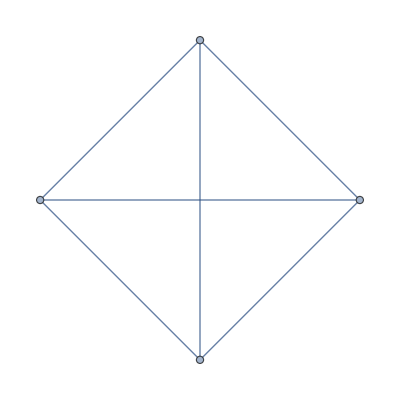

```mathematica
ReadGrof[1]
```

## This checks whether any 5-base can be embedded in an empty hexagon with a positive colofour

Starting 5

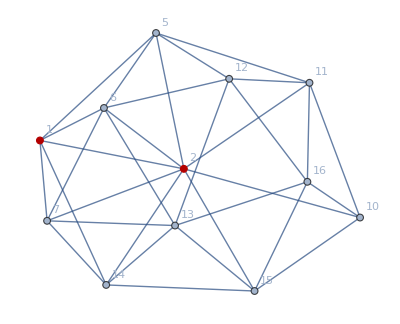
OEPS5     3     {1,2,4,8,9}     {1,2,4,8,9,10}     31984     -Graphics--19671594 x+92971055 x^2-201524291 x^3+268393565 x^4-247528009 x^5+168473872 x^6-87822730 x^7+35815950 x^8-11542314 x^9+2941552 x^10-587944 x^11+90456 x^12-10360 x^13+833 x^14-42 x^15+x^1698496 x-601344 x^2+1695600 x^3-2935200 x^4+3493092 x^5-3028800 x^6+1976021 x^7-986366 x^8+378782 x^9-111393 x^10+24696 x^11-4002 x^12+448 x^13-31 x^14+x^15-x+x^2-175560 x+671366 x^2-1128741 x^3+1115972 x^4-728015 x^5+331513 x^6-108142 x^7+25377 x^8-4210 x^9+471 x^10-32 x^11+x^12

```mathematica
values789Three=Monitor[
Table[
Print["Starting ", p];
With[{mainGraph=Graph[plantri[[p]]]},
Table[
v->
With[{
span=FindSpanningTree[VertexDelete[NeighborhoodGraph[mainGraph,v],v]]
},
Table[
With[
{f=VertexDelete[EdgeDelete[mainGraph,EdgeList[span]],v]},
Table[
{h["signature"],
With[
{i=EmbedGraphPlantri[f,h,vert]},
With[
{val=
ChromaticPolynomial[i,4]/24},
If[val==0,Print["OEPS",p,"     ", v,"     ",vert, "     ", VertexList[span],"     ",h["signature"],"     ",Graph[i,GraphHighlight->vert,VertexLabels->"Name"],ChromaticPolynomial[mainGraph,x],ChromaticPolynomial[f,x],ChromaticPolynomial[h["graph"],x],ChromaticPolynomial[i,x]]];
{p,v,vert,h["signature"],val}
]
]}
,
{h,Table[stubbornForm5[k],{k,Select[Sort[baseKeys5],#≠k5Key&]}]}
]
]
,{vert,Subsets[VertexList[span],{5}]}
]
]

,{v,Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==6&]}
]
],
{p,5,5}
],
{p,v,vert,h["signature"]}
];
```

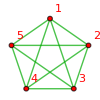
-Graphics-{29524→v1x2x3x4x5,0}No IH

```mathematica
CosyPrint5[29524]
```

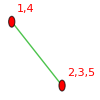
-Graphics-{31984→v14x235,1/2}No IH

```mathematica
CosyPrint5[31984]
```

```mathematica
Length[Intersection[stubbornKeys5,baseKeys5]]
```

26

```mathematica
ChromaticPolynomial[-Graphics-,x]
```

ChromaticPolynomial::graph: A graph object is expected at position 1 in Graph[{5, 6, 7, 10, 11, 12, 13, 14, 15, 16, 1, 2}, {Null, {{1, 5}, {1, 6}, {1, 2}, {2, 6}, {2, 7}, {2, 3}, {3, 7}, {3, 8}, {4, 9}, {4, 10}, {4, 5}, {5, 10}, {5, 6}, {6, 10}, {6, 7}, {7, 10}, {7, 9}, {7, 8}, {8, 9}, {9, 10}, {11, 1}, {11, 2}, {11, 3}, {11, 8}, {12, 1}, {12, 2}, {12, 3}, {12, 4}, {12, 5}, {12, 8}, {12, 9}, {11, 12}}}, {GridLinesStyle → Directive[InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.5`, 0.4`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.33333333333333337`, 0.4`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

ChromaticPolynomial[Graph[{5,6,7,10,11,12,13,14,15,16,1,2},{Null,{{1,5},{1,6},{1,2},{2,6},{2,7},{2,3},{3,7},{3,8},{4,9},{4,10},{4,5},{5,10},{5,6},{6,10},{6,7},{7,10},{7,9},{7,8},{8,9},{9,10},{11,1},{11,2},{11,3},{11,8},{12,1},{12,2},{12,3},{12,4},{12,5},{12,8},{12,9},{11,12}}},{GridLinesStyle→Directive[GrayLevel[0.5, 0.4]],GraphHighlight→{1,9,2,8,4},GraphLayout→{Dimension→2},VertexLabels→{Name}}],x]

```mathematica
EdgeList[-Graphics-]
```

EdgeList::graph: A graph object is expected at position 1 in Graph[{5, 6, 7, 10, 11, 12, 13, 14, 15, 16, 1, 2}, {Null, {{1, 5}, {1, 6}, {1, 2}, {2, 6}, {2, 7}, {2, 3}, {3, 7}, {3, 8}, {4, 9}, {4, 10}, {4, 5}, {5, 10}, {5, 6}, {6, 10}, {6, 7}, {7, 10}, {7, 9}, {7, 8}, {8, 9}, {9, 10}, {11, 1}, {11, 2}, {11, 3}, {11, 8}, {12, 1}, {12, 2}, {12, 3}, {12, 4}, {12, 5}, {12, 8}, {12, 9}, {11, 12}}}, {GridLinesStyle → Directive[InterpretationBox[ButtonBox[TooltipBox[GraphicsBox[List[List[GrayLevel[0], RectangleBox[List[0, 0]]], List[GrayLevel[0], RectangleBox[List[1, -1]]], List[GrayLevel[0.5`, 0.4`], RectangleBox[List[0, -1], List[2, 1]]]], Rule[AspectRatio, 1], Rule[Frame, True], Rule[FrameStyle, GrayLevel[0.33333333333333337`, 0.4`]], Rule[FrameTicks, None], Rule[PlotRangePadding, None], Rule[ImageSize, Dynamic[List[Automatic, Times[1.35`, CurrentValue[.

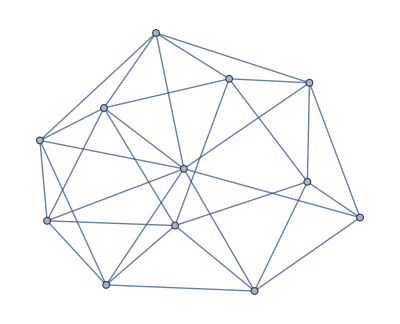

```mathematica
Graph[{5,6,7,10,11,12,13,14,15,16,1,2},{{1,5},{1,6},{1,2},{2,6},{2,7},{2,3},{3,7},{3,8},{4,9},{4,10},{4,5},{5,10},{5,6},{6,10},{6,7},{7,10},{7,9},{7,8},{8,9},{9,10},{11,1},{11,2},{11,3},{11,8},{12,1},{12,2},{12,3},{12,4},{12,5},{12,8},{12,9},{11,12}},GraphLayout->"SpringElectricalEmbedding"]
```

```mathematica
ChromaticPolynomial[Graph[{5,6,7,10,11,12,13,14,15,16,1,2},{{1,5},{1,6},{1,2},{2,6},{2,7},{2,3},{3,7},{3,8},{4,9},{4,10},{4,5},{5,10},{5,6},{6,10},{6,7},{7,10},{7,9},{7,8},{8,9},{9,10},{11,1},{11,2},{11,3},{11,8},{12,1},{12,2},{12,3},{12,4},{12,5},{12,8},{12,9},{11,12}}],x]
```

-175560 x+671366 x^2-1128741 x^3+1115972 x^4-728015 x^5+331513 x^6-108142 x^7+25377 x^8-4210 x^9+471 x^10-32 x^11+x^12

```mathematica
Roots[-175560 x+671366 x^2-1128741 x^3+1115972 x^4-728015 x^5+331513 x^6-108142 x^7+25377 x^8-4210 x^9+471 x^10-32 x^11+x^12==0,x]//N
```

x==0.||x==3.62215||x==2.39993-2.67918 ⅈ||x==2.39993+2.67918 ⅈ||x==3.26334-0.12883 ⅈ||x==3.26334+0.12883 ⅈ||x==3.52566-1.48482 ⅈ||x==3.52566+1.48482 ⅈ||x==1.||x==2.||x==3.||x==4.

```mathematica
ChromaticPolynomial[Graph[{1, 2}, {UndirectedEdge[1, 2]}],x]
```

ChromaticPolynomial::graph: A graph object is expected at position 1 in InterpretationBox[Cell[.

ChromaticPolynomial[Graph[{1, 2}, {UndirectedEdge[1, 2]}],x]

```mathematica
ChromaticPolynomial[Graph[{1,2},{UndirectedEdge[1,2]}],x]
```

-x+x^2

## Embed the alfa1 etc in a pentagon

## unfortunately this breaks down at plantri[[7]]

Starting 7

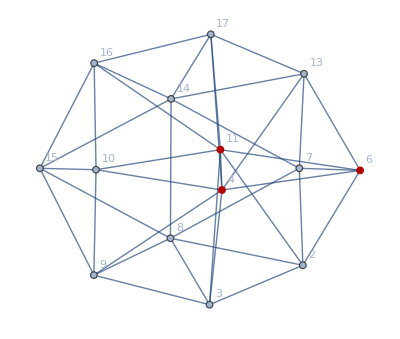
OEPS--7     5     {11,4,1,6,12}     {1,4,6,11,12}     {1<->4,1<->6,4<->11,6<->12}     36112     -Graphics-{72007008 x-355009664 x^2+808062888 x^3-1137507794 x^4+1116439755 x^5-814730131 x^6+459259781 x^7-204591612 x^8+72921212 x^9-20879569 x^10+4786675 x^11-868893 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17,-685584 x+4057560 x^2-11169468 x^3+19049250 x^4-22579600 x^5+19746792 x^6-13181157 x^7+6843713 x^8-2787381 x^9+890523 x^10-221290 x^11+41986 x^12-5885 x^13+575 x^14-35 x^15+x^16,2 x-3 x^2+x^3,-2997216 x+12457536 x^2-23236766 x^3+26071339 x^4-19815666 x^5+10854453 x^6-4434668 x^7+1374444 x^8-324190 x^9+57590 x^10-7496 x^11+677 x^12-38 x^13+x^14}

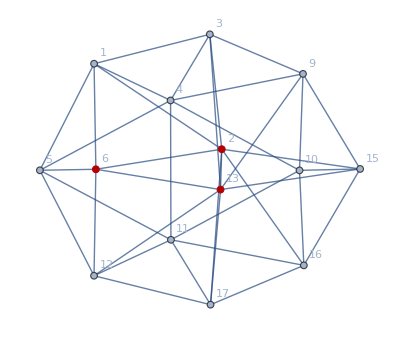
OEPS--7     7     {13,6,2,8,14}     {2,6,8,13,14}     {2<->6,2<->8,6<->13,8<->14}     31714     -Graphics-{72007008 x-355009664 x^2+808062888 x^3-1137507794 x^4+1116439755 x^5-814730131 x^6+459259781 x^7-204591612 x^8+72921212 x^9-20879569 x^10+4786675 x^11-868893 x^12+122328 x^13-12900 x^14+960 x^15-45 x^16+x^17,-685584 x+4057560 x^2-11169468 x^3+19049250 x^4-22579600 x^5+19746792 x^6-13181157 x^7+6843713 x^8-2787381 x^9+890523 x^10-221290 x^11+41986 x^12-5885 x^13+575 x^14-35 x^15+x^16,2 x-3 x^2+x^3,-2997216 x+12457536 x^2-23236766 x^3+26071339 x^4-19815666 x^5+10854453 x^6-4434668 x^7+1374444 x^8-324190 x^9+57590 x^10-7496 x^11+677 x^12-38 x^13+x^14}

```mathematica
values789Three=Monitor[
Table[
Print["Starting ", p];
With[{mainGraph=Graph[plantri[[p]]]},
p->Table[
v->
{
ChromaticPolynomial[mainGraph,4]/24,

With[
{neighbours=VertexDelete[NeighborhoodGraph[mainGraph,v],v]},
With[{
span=FindSpanningTree[neighbours]
},
With[
{vert=TreeToCycle[span],
f=VertexDelete[EdgeDelete[mainGraph,EdgeList[neighbours]],v]},
Table[
With[
{i=EmbedGraphPlantri[f,h,vert]},
With[
{val=
ChromaticPolynomial[i,4]/24},
If[val==0,Print["OEPS--",p,"     ", v,"     ",vert, "     ", VertexList[span],"     ",EdgeList[span],"     ",h["signature"],"     ",Graph[i,GraphHighlight->vert,VertexLabels->"Name"],{ChromaticPolynomial[mainGraph,x],ChromaticPolynomial[f,x],ChromaticPolynomial[h["graph"],x],ChromaticPolynomial[i,x]}]
];
{val,Graph[VertexDelete[mainGraph,v],
GraphHighlight->EdgeList[neighbours],
GraphLayout->"PlanarEmbedding", 
VertexLabels->"Name",
PlotLabel->h["vertexsets"]/.Table[k->vert[[k]],{k,Length[vert]}]]}
]
]
,
{h,Table[stubbornForm5[k],{k,{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}}]}
]
]
]
]
}
,{v,{5,7}(*Select[VertexList[mainGraph],VertexDegree[mainGraph,#]==5&]*)}
]
],
{p,7,7}
],
{p,v,h["signature"]}
];
```

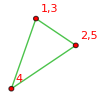
-Graphics-{36112→v13x25x4,1}No IH

```mathematica
CosyPrint5[delta1Key]
```

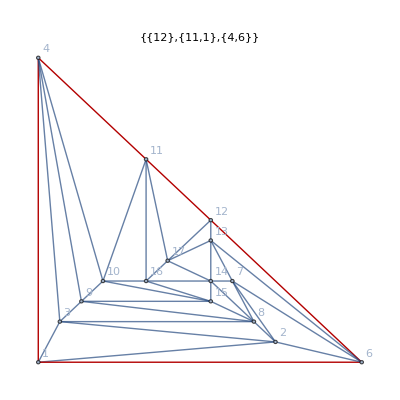
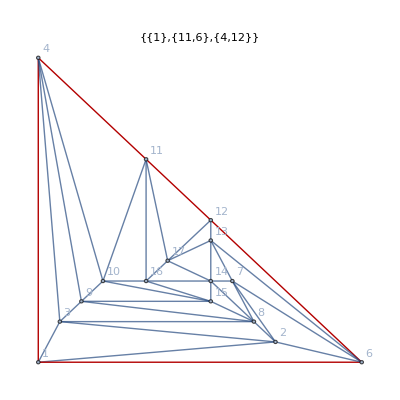
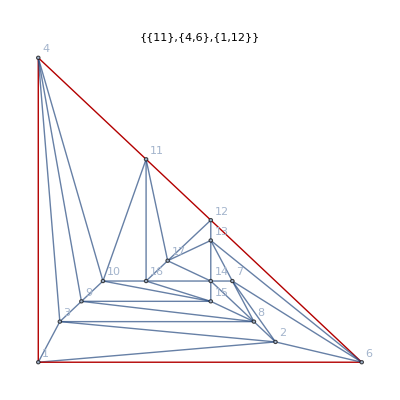
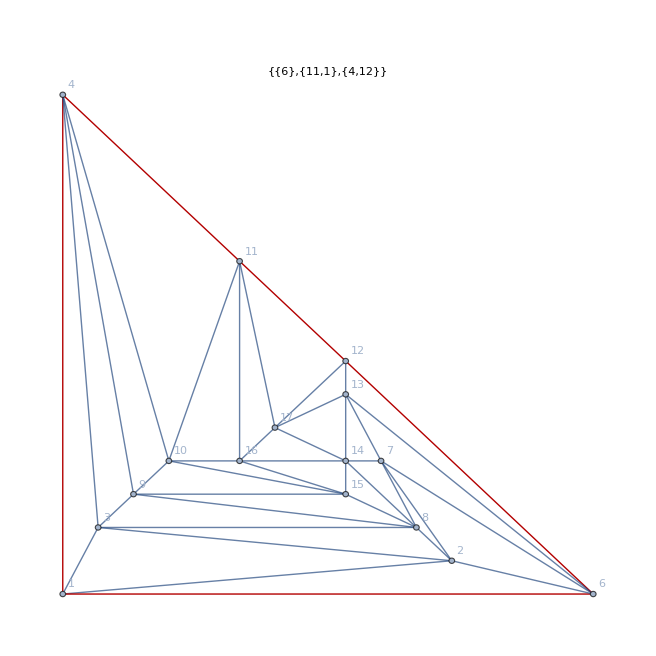
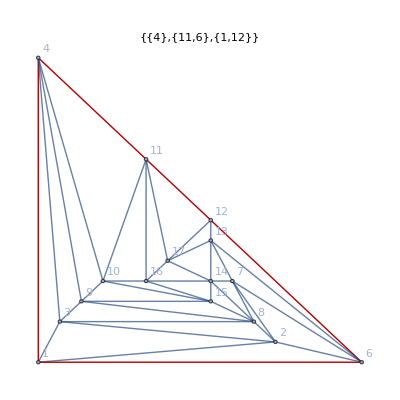
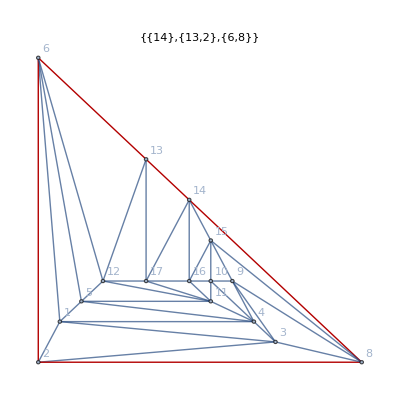
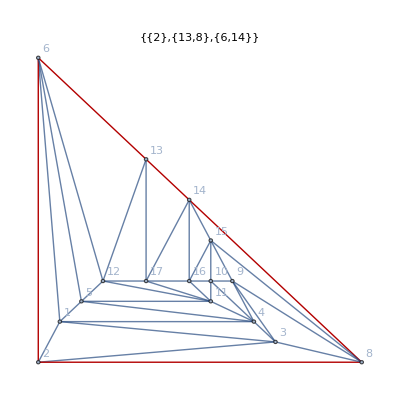
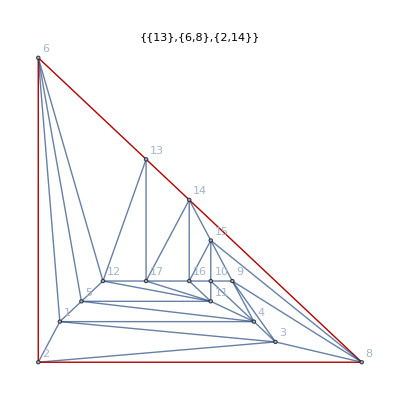
{7→{5→{16,{{3,-Graphics-},{3,-Graphics-},{5,-Graphics-},{0,-Graphics-},{5,-Graphics-}}},7→{16,{{5,-Graphics-},{3,-Graphics-},{3,-Graphics-},{5,-Graphics-},{0,-Graphics-}}}}}

```mathematica
values789Three
```

```mathematica
{alfa1Key,beta1Key,gamma1Key,delta1Key,epsilon1Key}
```

{36166,31738,29608,36112,31714}

```mathematica
Monitor[Table[{p,ChromaticPolynomial[Graph[plantri[[p]]],4]},{p,20,30}],p]
```

{{20,1272},{21,1152},{22,1248},{23,2016},{24,1536},{25,1152},{26,1248},{27,1920},{28,1728},{29,1560},{30,1200}}

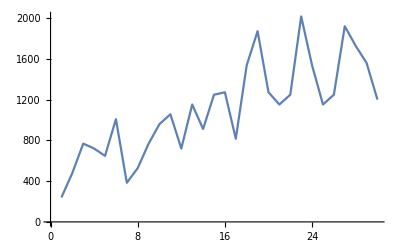

```mathematica
ListLinePlot[{{1,240},{2,480},{3,768},{4,720},{5,648},{6,1008},{7,384},{8,528},{9,768},{10,960},{11,1056},{12,720},{13,1152},{14,912},{15,1248},{16,1272},{17,816},{18,1536},{19,1872},{20,1272},{20,1272},{21,1152},{22,1248},{23,2016},{24,1536},{25,1152},{26,1248},{27,1920},{28,1728},{29,1560},{30,1200}}]
```

```mathematica
values789Three
```

{7→{1→{16,{4,2,5,2,3}},2→{16,{22,14,5,32,3}},3→{16,{32,2,16,12,6}},5→{16,{21,0,21,9,9}},7→{16,{31,5,21,11,12}},9→{16,{18,2,16,6,12}},10→{16,{12,4,16,12,8}},12→{16,{31,2,32,11,14}},13→{16,{31,5,20,22,12}},15→{16,{2,12,12,4,12}},16→{16,{4,14,6,6,14}},17→{16,{4,4,2,2,4}}}}

```mathematica
1/. 1->7
```

7

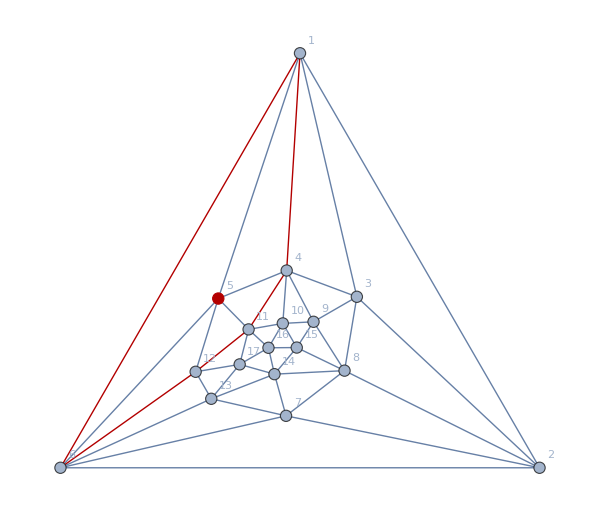

```mathematica
Graph[plantri[[7]],GraphHighlight->{5,1<->4,4<->11,11<->12,12<->6,6<->1},GraphLayout->"TutteEmbedding",VertexLabels->"Name",ImageSize->600]
```

## The following graph fails with a delta1 embedding (node 5 has been removed)

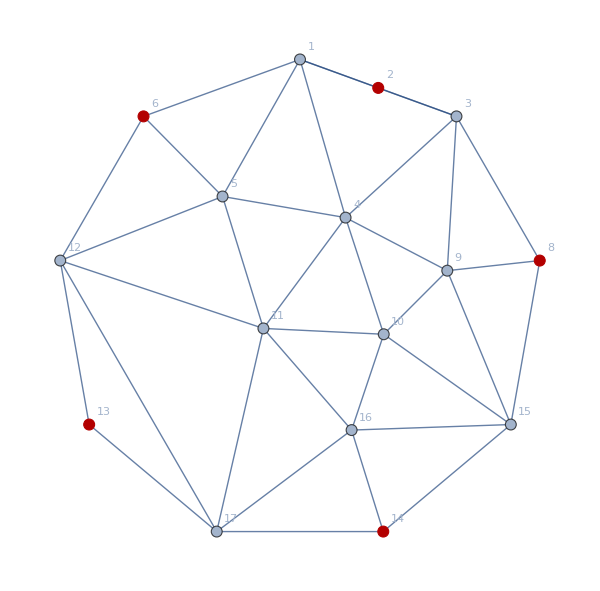

```mathematica
Graph[VertexDelete[EdgeDelete[Graph[plantri[[7]]],{2<->6,2<->8,6<->13,8<->14,13<->14}],7],GraphHighlight->{2,6,8,13,14},GraphLayout->"TutteEmbedding",VertexLabels->"Name",ImageSize->600]
```

## The following graph fails with a delta1 embedding (node 5 has been removed)

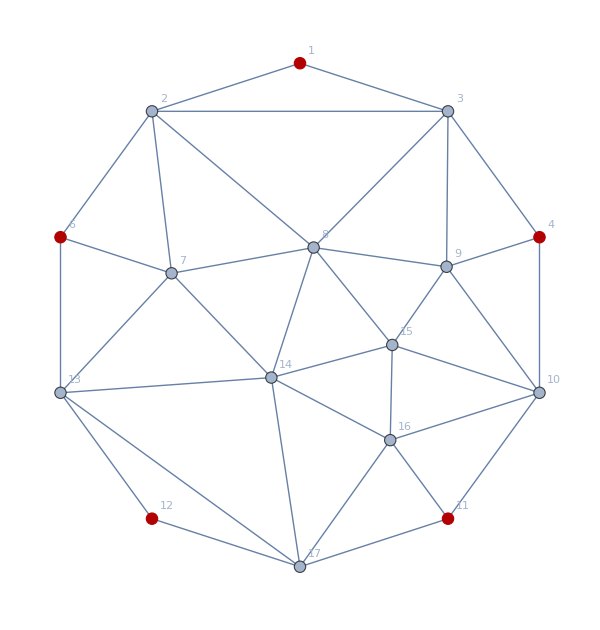

```mathematica
Graph[VertexDelete[EdgeDelete[Graph[plantri[[7]]],{1<->4,4<->11,11<->12,12<->6,6<->1}],5],GraphHighlight->{1,4,11,12,6},GraphLayout->"TutteEmbedding",VertexLabels->"Name",ImageSize->600]
```

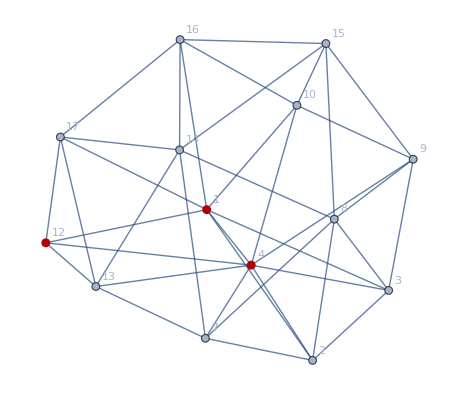

```mathematica
gg=Graph[EmbedGraphPlantri[VertexDelete[EdgeDelete[Graph[plantri[[7]]],{1<->4,4<->11,11<->12,12<->6,6<->1}],5],treeForm5[delta1Key],{1,4,11,12,6}],VertexLabels->"Name",GraphHighlight->{1,4,11,12,6}]
```

```mathematica
FindClique[gg]
```

{{2,3,1,4}}

```mathematica
EdgeList[gg]//Sort
```

{1<->2,1<->3,1<->4,1<->10,1<->16,1<->17,2<->3,2<->7,2<->8,3<->8,3<->9,4<->2,4<->3,4<->7,4<->9,4<->10,4<->13,7<->8,7<->13,7<->14,8<->9,8<->14,8<->15,9<->10,9<->15,10<->15,10<->16,12<->1,12<->4,12<->13,12<->17,13<->14,13<->17,14<->15,14<->16,14<->17,15<->16,16<->17}

```mathematica
ChromaticPolynomial[gg,x]
```

-2626218 x+11087091 x^2-21029741 x^3+23998279 x^4-18540964 x^5+10311318 x^6-4269931 x^7+1338683 x^8-318723 x^9+57028 x^10-7461 x^11+676 x^12-38 x^13+x^14

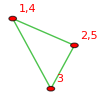
-Graphics-{31738→v14x25x3,1}No IH

```mathematica
CosyPrint5[beta1Key,treeForm5]
```

```mathematica
2 x-3 x^2+x^3-2997216 x+12457536 x^2-23236766 x^3+26071339 x^4-19815666 x^5+10854453 x^6-4434668 x^7+1374444 x^8-324190 x^9+57590 x^10-7496 x^11+677 x^12-38 x^13+x^14/.x->4
```

-40